```mathematica
(files=FileNames["*.xlsx",NotebookDirectory[]])
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx}

```mathematica
file1 = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx

```mathematica
(s = Import[file1])//InputForm;
```

```mathematica
s = s⟦1⟧;
```

```mathematica
data = (Interpreter["Number"][#]&/@s);
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"g2out.xlsx"},data]
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
files = FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx}

```mathematica
file2 = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx

```mathematica
s = Import[file2];
```

```mathematica
s =s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,100000.},{2.,100000.},{4.,100000.},{6.,100000.},{8.,100000.},{10.,100000.},{12.,100000.},{14.,100000.},{16.,100000.},{18.,100000.},{20.,100000.},{22.,100000.},{24.,100000.},{26.,100000.},{28.,100000.},{30.,25631.},{32.,9951.5},{34.,5388.4},{36.,2564.1},{38.,1371.7},3019,{6078.,20.84},{6080.,20.638},{6082.,20.303},{6084.,20.075},{6086.,19.757},{6088.,19.525},{6090.,19.427},{6092.,19.195},{6094.,18.98},{6096.,18.778},{6098.,18.559},{6100.,18.447},{6102.,18.228},{6104.,18.013},{6106.,17.794},{6108.,17.665},{6110.,17.45},{6112.,17.248},{6114.,17.132},{6116.,16.93},{6118.,16.715}}
 |  |  |  |

```mathematica
lm1 = LinearModelFit[s⟦1040;;1170⟧,{},x]
```

FittedModel[26278.3]

```mathematica
lm1 = Normal[lm1]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

26278.3

```mathematica
InputForm[pro]
```

{"AdjustedRSquared", "AIC", "AICc", "ANOVATable", "ANOVATableDegreesOfFreedom", "ANOVATableEntries", "ANOVATableFStatistics", "ANOVATableMeanSquares", "ANOVATablePValues", "ANOVATableSumsOfSquares", 
 "BasisFunctions", "BetaDifferences", "BestFit", "BestFitParameters", "BIC", "CatcherMatrix", "CoefficientOfVariation", "CookDistances", "CorrelationMatrix", "CovarianceMatrix", "CovarianceRatios", 
 "Data", "DesignMatrix", "DurbinWatsonD", "EigenstructureTable", "EigenstructureTableEigenvalues", "EigenstructureTableEntries", "EigenstructureTableIndexes", "EigenstructureTablePartitions", 
 "EstimatedVariance", "FitDifferences", "FitResiduals", "Function", "FVarianceRatios", "HatDiagonal", "MeanPredictionBands", "MeanPredictionConfidenceIntervals", 
 "MeanPredictionConfidenceIntervalTable", "MeanPredictionConfidenceIntervalTableEntries", "MeanPredictionErrors", "ParameterConfidenceIntervals", "ParameterConfidenceIntervalTable", 
 "ParameterConfidenceIntervalTableEntries", "ParameterConfidenceRegion", "ParameterErrors", "ParameterPValues", "ParameterTable", "ParameterTableEntries", "ParameterTStatistics", 
 "PartialSumOfSquares", "PredictedResponse", "Properties", "Response", "RSquared", "SequentialSumOfSquares", "SingleDeletionVariances", "SinglePredictionBands", "SinglePredictionConfidenceIntervals", 
 "SinglePredictionConfidenceIntervalTable", "SinglePredictionConfidenceIntervalTableEntries", "SinglePredictionErrors", "StandardizedResiduals", "StudentizedResiduals", "VarianceInflationFactors"}

```mathematica
lm1 = LinearModelFit[Join[s⟦1040;;1170⟧,s⟦1480;;1540⟧],{},x]
otl = lm1["FitResiduals"]
lm1["ParameterTable"]
lm1["ParameterConfidenceIntervalTable"];
lm1["ParameterConfidenceIntervalTableEntries"];
lm1["ParameterErrors"];
lm1["FitDifferences"];
lm1["AdjustedRSquared"];
lm1= Normal[lm1];
```

FittedModel[27457.2]

{215.771,215.771,215.771,262.771,215.771,215.771,215.771,262.771,202.771,249.771,249.771,249.771,249.771,81.7708,81.7708,-100.229,-147.229,-100.229,-254.229,-388.229,-435.229,-449.229,-590.229,-590.229,-590.229,-731.229,-731.229,-731.229,-792.229,-731.229,-765.229,-926.229,-926.229,-926.229,-1067.23,-1067.23,-1248.23,-1248.23,-1443.23,-1383.23,-1430.23,-1383.23,-1383.23,-1383.23,-1430.23,-1383.23,-1430.23,-1564.23,-1578.23,-1578.23,-1578.23,-1578.23,-1578.23,-1578.23,-1578.23,-1564.23,-1564.23,-1564.23,-1625.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1719.23,-1584.23,-1584.23,-1584.23,-1584.23,-1584.23,-1584.23,-1746.23,-1746.23,-1564.23,-1564.23,-1564.23,-1564.23,-1544.23,-1719.23,-1605.23,-1605.23,-1544.23,-1544.23,-1544.23,-1544.23,-1544.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1759.23,-1544.23,-1544.23,-1544.23,-1544.23,-1605.23,-1517.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1564.23,-1423.23,-1363.23,-1564.23,-1383.23,-1383.23,-1383.23,-1383.23,-1383.23,-1383.23,-1383.23,-1383.23,-1369.23,-1383.23,-1228.23,-1403.23,-1403.23,-1403.23,3964.77,3649.77,3649.77,3649.77,3528.77,3528.77,3326.77,3528.77,3528.77,3353.77,3353.77,3172.77,3010.77,3010.77,3010.77,3010.77,3010.77,3010.77,3010.77,2856.77,2809.77,2856.77,2856.77,2856.77,2856.77,2674.77,2674.77,2513.77,2513.77,2338.77,2338.77,2359.77,2359.77,2177.77,2177.77,2177.77,2177.77,1996.77,1996.77,2157.77,1976.77,2023.77,2023.77,2023.77,1935.77,1982.77,1982.77,1996.77,1996.77,1996.77,1841.77,1841.77,1841.77,1841.77,1841.77,1841.77,1680.77,1680.77,1680.77,1680.77,1680.77}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 27457.2 | 132.91 | 206.585 | 1.70407×10^-226

```mathematica
sum = Sum[(otl⟦i⟧)^2,{i,1,Length@otl}]
```

6.47815×10^8

```mathematica
error  = Sqrt[sum/Length@otl]
```

1836.86

```mathematica
Properties[LinearModelFit]
```

Properties[LinearModelFit]

```mathematica
lm2 = LinearModelFit[Join[s⟦1180;;1230⟧,s⟦1550;;1570⟧],{},x]
lm2["ParameterTable"]
otl = lm2["FitResiduals"]
lm2 = Normal[lm2]
```

FittedModel[23188.]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 23188. | 201.592 | 115.024 | 1.98133×10^-82

{-787.986,-902.986,-902.986,-902.986,-902.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-752.986,-787.986,-787.986,-787.986,-787.986,-752.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-667.986,-632.986,-632.986,-632.986,-667.986,-632.986,-667.986,-667.986,-667.986,-517.986,-632.986,-632.986,-632.986,-632.986,-632.986,-632.986,-517.986,-517.986,5816.01,5654.01,6870.01,7643.01,1027.01,757.014,757.014,757.014,757.014,642.014,642.014,642.014,642.014,642.014,607.014,642.014,597.014,642.014,642.014,597.014,642.014}

23188.

```mathematica
otl
```

{-787.986,-902.986,-902.986,-902.986,-902.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-752.986,-787.986,-787.986,-787.986,-787.986,-752.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-787.986,-667.986,-632.986,-632.986,-632.986,-667.986,-632.986,-667.986,-667.986,-667.986,-517.986,-632.986,-632.986,-632.986,-632.986,-632.986,-632.986,-517.986,-517.986,5816.01,5654.01,6870.01,7643.01,1027.01,757.014,757.014,757.014,757.014,642.014,642.014,642.014,642.014,642.014,607.014,642.014,597.014,642.014,642.014,597.014,642.014}

```mathematica
sum  = Total[otl^2]
```

2.07748×10^8

```mathematica
error = Sqrt[sum/Length[otl]]
```

1698.64

```mathematica
lm3 = LinearModelFit[Join[s⟦1230;;1320⟧,s⟦1580;;1630⟧],{},x]
otl = lm3["FitResiduals"]
lm3 = Normal[lm3]
```

FittedModel[17114.]

{5556.04,5556.04,9478.04,161.042,-393.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-506.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-393.958,-359.958,-307.958,-281.958,-281.958,-307.958,-307.958,-307.958,-307.958,-307.958,-307.958,-206.958,-206.958,-206.958,-206.958,-206.958,-206.958,-198.958,-224.958,-224.958,-217.958,-217.958,-217.958,-217.958,-217.958,-217.958,-217.958,-307.958,-206.958,1417.04,172.042,172.042,198.042,198.042,198.042,172.042,172.042,206.042,206.042,172.042,198.042,198.042,172.042,172.042,198.042,198.042,198.042,172.042,172.042,198.042,198.042,198.042,198.042,198.042,198.042,198.042,198.042,198.042,198.042,198.042,172.042,172.042,172.042,198.042,198.042,198.042,172.042,172.042,258.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042,285.042}

17114.

```mathematica
sum = Total[otl^2]
```

1.69683×10^8

```mathematica
error = Sqrt[sum/Length[otl]]
```

1093.14

```mathematica
s⟦1;;3⟧
```

{{,},{0.,100000.},{2.,100000.}}

```mathematica
s⟦5;;6⟧
```

{{6.,100000.},{8.,100000.}}

```mathematica
Join[s⟦1;;3⟧,s⟦5;;6⟧]
```

{{,},{0.,100000.},{2.,100000.},{6.,100000.},{8.,100000.}}

```mathematica
Total
```

26278.3[FitResiduals]

```mathematica
(*,RegionFunction->Function[{x},x>2100]*)
```

```mathematica
Show[ListPlot[s⟦1000;;1700⟧,GridLines->{Range[0,4000,20], Range[0,110000,2000]}],Plot[lm1,{x,2080,2340},PlotStyle->Red,PlotLabels->lm1],Plot[lm2,{x,2350,2460},PlotLabels->lm2,PlotStyle->Red],Plot[lm3,{x,2460,2640},PlotStyle->Red,PlotLabels->lm3],Plot[lm1,{x,2960,3100},PlotStyle->Red,PlotLabels->lm1],Plot[lm2,{x,3103,3146},PlotLabels->lm2,PlotStyle->Red],Plot[lm3,{x,3155,3269},PlotStyle->Red,PlotLabels->lm3]]
```

```mathematica
files
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx}

```mathematica
fil3 = files⟦4⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
s = Import[fil3];
```

```mathematica
s=s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,9.9×10^9},{2.,9.9×10^9},{4.,9.9×10^9},{6.,9.9×10^9},{8.,9.9×10^9},{10.,9.9×10^9},{12.,9.9×10^9},{14.,9.9×10^9},{16.,9.9×10^9},{18.,9.9×10^9},{20.,9.9×10^9},{22.,9.9×10^9},{24.,9.9×10^9},{26.,9.9×10^9},{28.,9.9×10^9},{30.,9.9×10^9},{32.,9.9×10^9},{34.,9.9×10^9},{36.,9.9×10^9},{38.,9.9×10^9},{40.,9.9×10^9},{42.,9.9×10^9},3014,{6072.,9.9×10^9},{6074.,9.9×10^9},{6076.,9.9×10^9},{6078.,9.9×10^9},{6080.,9.9×10^9},{6082.,9.9×10^9},{6084.,9.9×10^9},{6086.,9.9×10^9},{6088.,9.9×10^9},{6090.,9.9×10^9},{6092.,9.9×10^9},{6094.,9.9×10^9},{6096.,9.9×10^9},{6098.,9.9×10^9},{6100.,9.9×10^9},{6102.,9.9×10^9},{6104.,9.9×10^9},{6106.,9.9×10^9},{6108.,9.9×10^9},{6110.,9.9×10^9},{6112.,9.9×10^9},{6114.,9.9×10^9},{6116.,9.9×10^9}}
 |  |  |  |

```mathematica
line=LinearModelFit[s⟦2230;;2290⟧,{1,x},x]
line["ParameterTable"]
line = Normal[line]
```

FittedModel[-11.4864+0.00257531 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11.4864 | 0.069071 | -166.299 | 1.56846×10^-80
x | 0.00257531 | 0.0000152943 | 168.384 | 7.53109×10^-81

-11.4864+0.00257531 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11.4864 | 0.069071 | -166.299 | 1.56846×10^-80
x | 0.00257531 | 0.0000152943 | 168.384 | 7.53109×10^-81

-11.4864+0.00257531 x

```mathematica
line2=LinearModelFit[s⟦2340;;2390⟧,{1,x},x]
line2["ParameterTable"]
line2= Normal[line2]
```

FittedModel[-11.9907+0.00256893 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11.9907 | 0.0396994 | -302.037 | 8.6271×10^-82
x | 0.00256893 | 8.40005×10^-6 | 305.823 | 4.68714×10^-82

-11.9907+0.00256893 x

```mathematica
ListPlot[s⟦2200;;2400⟧,GridLines->{Range[4000,5000,20], Range[0,0.5,0.01]}]
```

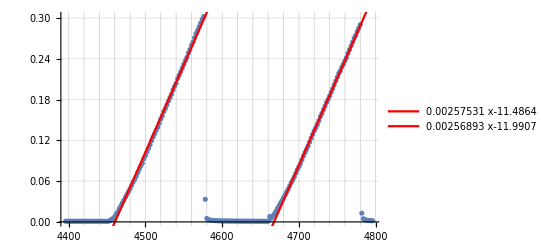

```mathematica
Show[ListPlot[s⟦2200;;2400⟧,GridLines->{Range[4000,5000,20], Range[0,0.5,0.01]}],Plot[{line,line2},{x,4400,4800},PlotStyle->Red,PlotLegends->{line,line2}]]
```

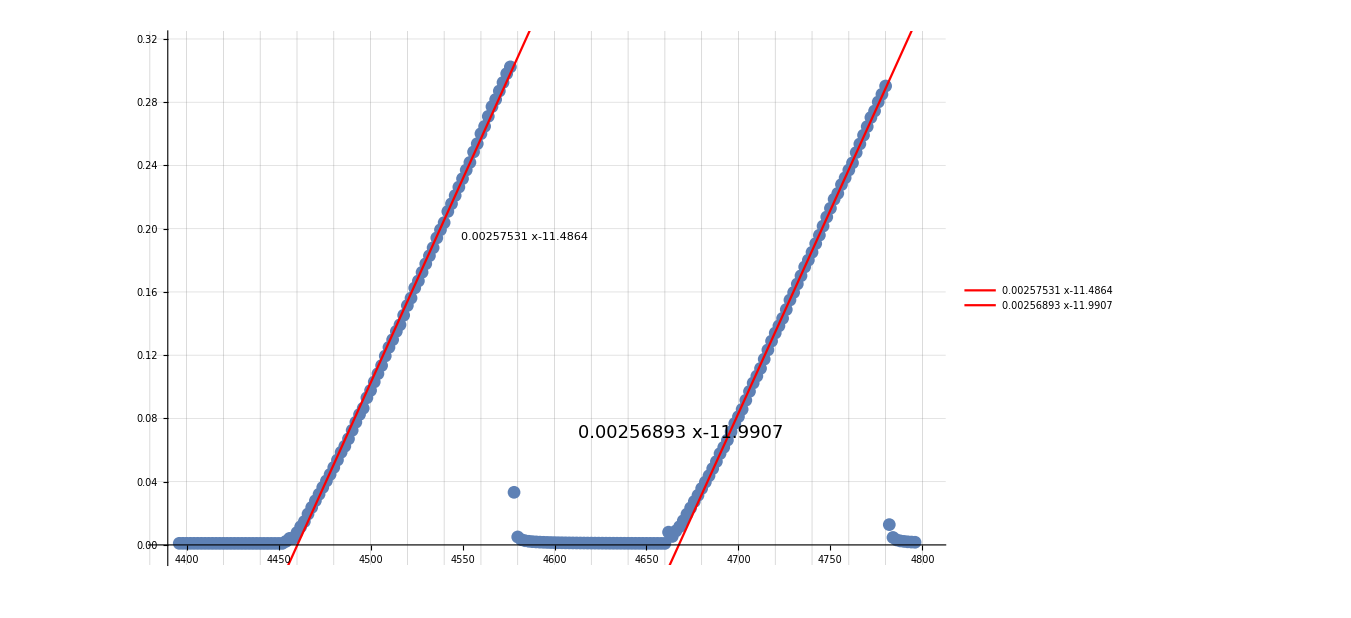

```mathematica
file2
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx

```mathematica
(s = Import[file2])//InputForm;
```

```mathematica
s = s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,100000.},{2.,100000.},{4.,100000.},{6.,100000.},{8.,100000.},{10.,100000.},{12.,100000.},{14.,100000.},{16.,100000.},{18.,100000.},{20.,100000.},{22.,100000.},{24.,100000.},{26.,100000.},{28.,100000.},{30.,25631.},{32.,9951.5},{34.,5388.4},{36.,2564.1},{38.,1371.7},3019,{6078.,20.84},{6080.,20.638},{6082.,20.303},{6084.,20.075},{6086.,19.757},{6088.,19.525},{6090.,19.427},{6092.,19.195},{6094.,18.98},{6096.,18.778},{6098.,18.559},{6100.,18.447},{6102.,18.228},{6104.,18.013},{6106.,17.794},{6108.,17.665},{6110.,17.45},{6112.,17.248},{6114.,17.132},{6116.,16.93},{6118.,16.715}}
 |  |  |  |

```mathematica
s⟦2;;All⟧
```

{{0.,100000.},{2.,100000.},{4.,100000.},{6.,100000.},{8.,100000.},{10.,100000.},{12.,100000.},{14.,100000.},{16.,100000.},{18.,100000.},{20.,100000.},{22.,100000.},{24.,100000.},{26.,100000.},{28.,100000.},{30.,25631.},{32.,9951.5},{34.,5388.4},{36.,2564.1},{38.,1371.7},{40.,728.82},3018,{6078.,20.84},{6080.,20.638},{6082.,20.303},{6084.,20.075},{6086.,19.757},{6088.,19.525},{6090.,19.427},{6092.,19.195},{6094.,18.98},{6096.,18.778},{6098.,18.559},{6100.,18.447},{6102.,18.228},{6104.,18.013},{6106.,17.794},{6108.,17.665},{6110.,17.45},{6112.,17.248},{6114.,17.132},{6116.,16.93},{6118.,16.715}}
 |  |  |  |

```mathematica
s⟦All,2⟧ = Log@s⟦All,2⟧;
```

```mathematica
s
```

{{,Log[]},{0.,11.5129},{2.,11.5129},{4.,11.5129},{6.,11.5129},{8.,11.5129},{10.,11.5129},{12.,11.5129},{14.,11.5129},{16.,11.5129},{18.,11.5129},{20.,11.5129},{22.,11.5129},3035,{6094.,2.94339},{6096.,2.93269},{6098.,2.92095},{6100.,2.9149},{6102.,2.90296},{6104.,2.89109},{6106.,2.87886},{6108.,2.87159},{6110.,2.85934},{6112.,2.8477},{6114.,2.84095},{6116.,2.82909},{6118.,2.81631}}
 |  |  |  |

```mathematica
line=LinearModelFit[s⟦100;;170⟧,{1,x},x]
line["ParameterTable"]
line = Normal[line]
```

FittedModel[2.97978-0.0019021 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.97978 | 0.00880245 | 338.518 | 7.43425×10^-113
x | -0.0019021 | 0.0000327059 | -58.1577 | 2.31749×10^-60

2.97978-0.0019021 x

```mathematica
Show[ListPlot[s⟦100;;180⟧,GridLines->{Range[80,400,5], Range[2,4,0.01]}],Plot[line,{x,200,340},PlotLabels->line,PlotStyle->Red]]
```

```mathematica
files
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2.xlsx}

```mathematica
file = files⟦4⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
s = Import[file];
```

```mathematica
s= s⟦1⟧;
```

```mathematica
s⟦All,2⟧ = Log@s⟦All,2⟧;
```

```mathematica
s
```

{{,Log[]},{0.,23.0158},{2.,23.0158},{4.,23.0158},{6.,23.0158},{8.,23.0158},{10.,23.0158},{12.,23.0158},{14.,23.0158},{16.,23.0158},{18.,23.0158},{20.,23.0158},{22.,23.0158},3034,{6092.,23.0158},{6094.,23.0158},{6096.,23.0158},{6098.,23.0158},{6100.,23.0158},{6102.,23.0158},{6104.,23.0158},{6106.,23.0158},{6108.,23.0158},{6110.,23.0158},{6112.,23.0158},{6114.,23.0158},{6116.,23.0158}}
 |  |  |  |

```mathematica
line=LinearModelFit[s⟦1909;;1950⟧,{1,x},x]
line["ParameterTable"]
line = Normal[line]
```

FittedModel[146.639-0.0392164 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 146.639 | 9.78728 | 14.9826 | 5.31288×10^-18
x | -0.0392164 | 0.0025388 | -15.4468 | 1.86896×10^-18

146.639-0.0392164 x

```mathematica
Show[ListPlot[s⟦1909;;1950⟧,GridLines->{Range[3000,6000,5], Range[-10,0,0.5]}],Plot[line,{x,0,3890},PlotLegends->line,PlotStyle->Red]]
```

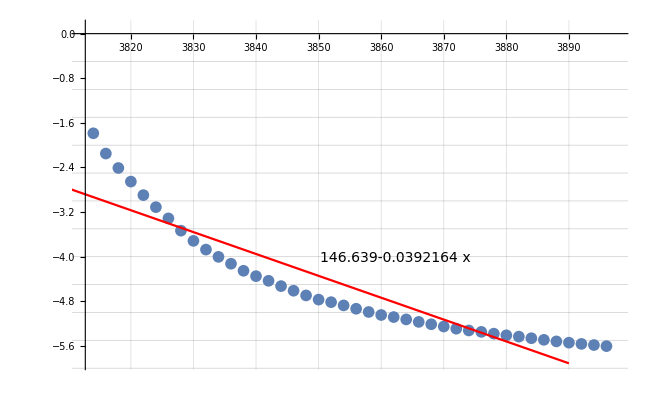

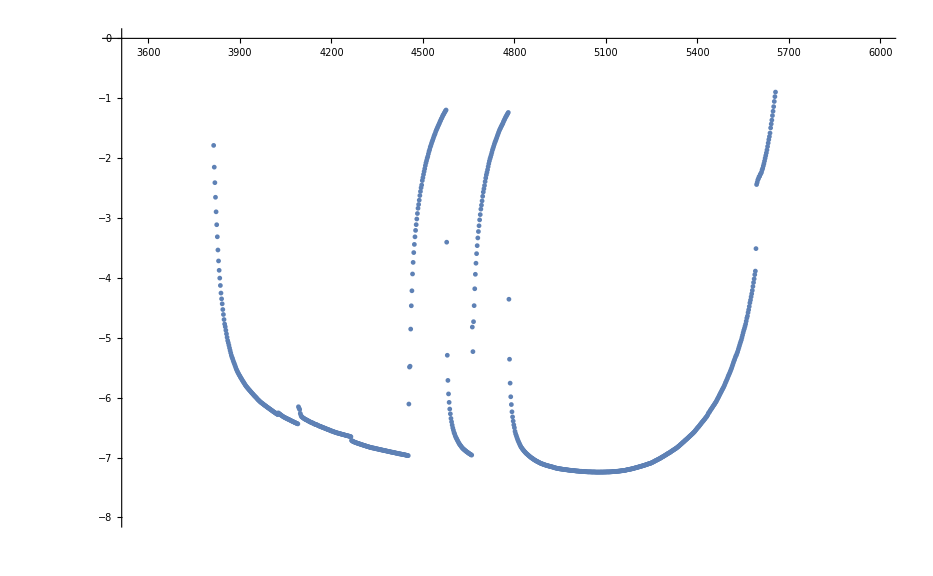

```mathematica
ListPlot[s,PlotRange->{{3500,6000},{-8,0}}]
```

```mathematica
|
```